Application I: ϕ^4-theory

This notebook demonstrates how to use the following packages:
	Basis-Scalar.wl
	MatrixElements-Scalar.wl
to generate the basis and matrix elements for ϕ^4 theory. We also show how to use the output data to reproduce Figures 12-17 in the paper.

# Set DMAX and Directory (RUN FIRST)

EVALUATE THIS CELL FIRST
This notebook is designed such that you construct and save the basis and matrix elements once, for some large value DMAX, then always use those reference files to extract data for any Δmax ≤ DMAX. This cell sets the value of DMAX, which will be used in all later computations, as well as the directory for saving / loading files (by default, it is set to the notebook directory).
By default, we have set DMAX=20, which limits the runtime and resulting file sizes. To accurately reproduce the figures in the paper, the user should set DMAX=40.

```mathematica
DMAX=20;
SetDirectory[NotebookDirectory[]];
```

# Generate Basis and Matrix Elements

## Generate Basis

```mathematica
(* Load 'Basis-Scalar.wl' (the scalar basis generation code). *)
Get["Basis-Scalar.wl"];

(* Set the precision to use for orthogonalization *)
precision=50;

(* Compute scalar basis using the function 'computeBosonBasis'. Output is two new variables:
basisBoson = the orthonormalized basis (what we want)
basisBosonPre = pre-orthogonalization (not needed)
Additionally, timing data is printed for each particle number n. *) 
computeBosonBasis[DMAX,precision];

(* This function saves variables in WXF format *)
binarySave[name_,expr_]:=Export[name<>".WXF",BinarySerialize[expr]];

(* Save 'basisBoson' *)
binarySave["BasisBosonD"<>ToString[DMAX],N[basisBoson]];
```

t=0.00001

n@ 1

t=0.00019

n@ 2

t=0.02909

n@ 3

t=0.093231

n@ 4

t=0.21902

n@ 5

t=0.33658

n@ 6

t=0.432617

n@ 7

t=0.506726

n@ 8

t=0.568139

n@ 9

t=0.611068

n@ 10

t=0.641472

n@ 11

t=0.662696

n@ 12

t=0.677639

n@ 13

t=0.689462

n@ 14

t=0.698981

n@ 15

t=0.707628

n@ 16

t=0.713852

n@ 17

t=0.718231

n@ 18

t=0.721507

n@ 19

t=0.723711

n@ 20

t=0.725027

## Generate Matrix Elements

```mathematica
(* These functions help save and load WXF formats *)
binarySave[name_,expr_]:=Export[name<>".WXF",BinarySerialize[expr]];
binaryGet[name_]:=Import[name]//BinaryDeserialize;

(* Load 'MatrixElements-Scalar.wl' (the scalar matrix element generation code). *)
Get["MatrixElements-Scalar.wl"];

(* Load basis file for given Δmax (see 'Generate Basis' section of this notebook) *)
basisBoson=binaryGet["BasisBosonD"<>ToString[DMAX]<>".WXF"];

(* Use the functions in 'MatrixElements-Scalar.wl' to compute Hamiltonian matrices: *)

(* Generate mass matrix. Output is the variable 'fullMassMatrix'. Timing data printed for each particle number n. *)
ComputeScalarMassMatrix[DMAX,basisBoson] ;

(* Generate ϕ^4 (n->n) matrix. Output is the variable 'fullPhi4NtoNMatrix'. Timing data printed for each particle number n. *)
ComputePhi4NtoNMatrix[DMAX,basisBoson]

(* Generate ϕ^4 (n->n+2) matrix. Output is the variable 'fullPhi4NtoNPlus2Matrix'. Timing data printed for each particle number n. *)
ComputePhi4NtoNPlus2Matrix[DMAX,basisBoson]

(* Save output *)
binarySave["ScalarMassD"<>ToString[DMAX],fullMassMatrix];
binarySave["ScalarPhi4NtoND"<>ToString[DMAX],fullPhi4NtoNMatrix];
binarySave["ScalarPhi4NtoN2D"<>ToString[DMAX],fullPhi4NtoNPlus2Matrix];
```

t=0.02577

@ n=1

t=0.072884

@ n=2

t=0.12927

@ n=3

t=0.26715

@ n=4

t=0.444828

@ n=5

t=0.653168

@ n=6

t=0.829585

@ n=7

t=0.965634

@ n=8

t=1.07016

@ n=9

t=1.15567

@ n=10

t=1.20537

@ n=11

t=1.2381

@ n=12

t=1.25818

@ n=13

t=1.27042

@ n=14

t=1.28196

@ n=15

t=1.28763

@ n=16

t=1.29151

@ n=17

t=1.29373

@ n=18

t=1.29557

@ n=19

t=1.29658

@ n=20

t=0.01709

@ n=2

t=0.12441

@ n=3

t=0.494015

@ n=4

t=1.07214

@ n=5

t=1.69906

@ n=6

t=2.21828

@ n=7

t=2.60394

@ n=8

t=2.83842

@ n=9

t=2.99417

@ n=10

t=3.09642

@ n=11

t=3.16494

@ n=12

t=3.20197

@ n=13

t=3.22128

@ n=14

t=3.23063

@ n=15

t=3.23606

@ n=16

t=3.23924

@ n=17

t=3.24136

@ n=18

t=3.24262

@ n=19

t=3.24352

@ n=20

t=0.01545

@ n=3

t=0.071155

@ n=4

t=0.25747

@ n=5

t=0.543626

@ n=6

t=0.865687

@ n=7

t=1.15389

@ n=8

t=1.39687

@ n=9

t=1.56616

@ n=10

t=1.68145

@ n=11

t=1.76495

@ n=12

t=1.81753

@ n=13

t=1.84453

@ n=14

t=1.86036

@ n=15

t=1.86843

@ n=16

t=1.8737

@ n=17

t=1.8775

@ n=18

t=1.87931

@ n=19

t=1.8805

@ n=20

# Diagonalize Hamiltonian and Reproduce Figures

## Mass Gap vs Coupling (Figure 12)

## Load Data

```mathematica
(* Load Hamiltonian matrices. These matrices include both odd and even particle-number states. *)
binaryGet[name_]:=Import[name]//BinaryDeserialize;
SetDirectory[NotebookDirectory[]];
fullMassMatrix=binaryGet["ScalarMassD"<>ToString[DMAX]<>".WXF"];                        (* Mass Matrix *)
fullNtoNMatrix=binaryGet["ScalarPhi4NtoND"<>ToString[DMAX]<>".WXF"];               (* ϕ^4(n->n) *)
fullNtoN2Matrix=binaryGet["ScalarPhi4NtoN2D"<>ToString[DMAX]<>".WXF"];         (* ϕ^4(n->n+2) *)
```

## Compute Mass Gap vs Coupling for Odd-Particle Sector

### Define useful functions

```mathematica
(* 'massFuncOdd' extracts the mass matrix for the odd-particle-number sector given 'fullMassMatrix'.
DMAX = max scaling dimension in 'fullMassMatrix'.
Dmax = desired Δmax to study (should be ≤ DMAX). *) 
massFuncOdd[DMAX_,Dmax_]:=Module[{i,j,Nmax,count,COUNT,massTemp},
Nmax=Ceiling[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n-1}]//Length,{n,Nmax}];
COUNT=Accumulate[Table[IntegerPartitions[DMAX,{n}]//Length,{n,0,2Nmax-2}]][[;;;;2]];
massTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(* 'intFuncOdd' extracts the ϕ^4 interaction matrix for the odd-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix'.
DMAX = max scaling dimension in 'fullNtoNMatrix' and 'fullNtoN2Matrix'.
Dmax = desired Δmax to study (should be ≤ DMAX). *)
intFuncOdd[DMAX_,Dmax_]:=Module[{i,j,Nmax,count,COUNT,intTemp},
Nmax=Ceiling[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n-1}]//Length,{n,Nmax}];
COUNT=Accumulate[Table[IntegerPartitions[DMAX,{n}]//Length,{n,0,2Nmax-2}]][[;;;;2]];
intTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=fullNtoNMatrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i+1]]+1;;COUNT[[i+1]]+count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[COUNT[[i+1]]+1;;COUNT[[i+1]]+count[[i+1]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];
```

### Compute lowest eigenvalues vs coupling and make plot

```mathematica
Dmax=20;                          (* Dmax = desired Δmax to study (should be ≤ DMAX) *) 
nPoints=2;                      (* How many low eigenvalues to compute for each value of the coupling λ *)

(* To efficiently compute the lowest eigenvalues, it is useful if all eigenvalues are positive. To ensure all eigenvalues are positive, we can add a small overall shift to the eigenvalues before diagonalizing the Hamitonian, then remove this shift after diagonalizing. This shift needs to be large enough to overcome any negative eigenvalues, but small enough to not decrease the precision of the resulting eigenvalues (in practice 50 is generally a safe value) *)
shift=50;

m=1;
λmax=2.4;
λmin=0.;
λcount=25;
dλ=(λmax-λmin)/(λcount-1)//N;
λlist=Table[λmin+dλ*(i-1),{i,λcount}];
mass=massFuncOdd[DMAX,Dmax];
int=intFuncOdd[DMAX,Dmax];

valListOdd=Table[{},{i,Length[λlist]}];
Monitor[For[iL=1,iL≤Length[λlist],iL++,
vals=Eigenvalues[SparseArray[N[full[m^2,4π λlist[[iL]],mass,int]+shift*IdentityMatrix[mass//Length]]],-nPoints,Method->"Arnoldi"];
valListOdd[[iL]]=vals-shift;
],{iL}];

dataOdd=Table[Thread[{λlist,valListOdd[[All,iM]]}],{iM,nPoints}];
```

## Compute Mass Gap vs Coupling for Even-Particle Sector

### Define useful functions

```mathematica
(* 'massFuncEven' extracts the mass matrix for the even-particle-number sector given 'fullMassMatrix'.
DMAX = max scaling dimension in 'fullMassMatrix'.
Dmax = desired Δmax to study (should be ≤ DMAX). *) 
massFuncEven[DMAX_,Dmax_]:=Module[{i,j,Nmax,count,COUNT,massTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
COUNT=Accumulate[Table[IntegerPartitions[DMAX,{n}]//Length,{n,1,2Nmax-1}]][[;;;;2]];
massTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(* 'intFuncEven' extracts the ϕ^4 interaction matrix for the even-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix'.
DMAX = max scaling dimension in 'fullNtoNMatrix' and 'fullNtoN2Matrix'.
Dmax = desired Δmax to study (should be ≤ DMAX). *)
intFuncEven[DMAX_,Dmax_]:=Module[{i,j,Nmax,count,COUNT,intTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
COUNT=Accumulate[Table[IntegerPartitions[DMAX,{n}]//Length,{n,1,2Nmax-1}]][[;;;;2]];
intTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=fullNtoNMatrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i+1]]+1;;COUNT[[i+1]]+count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[COUNT[[i+1]]+1;;COUNT[[i+1]]+count[[i+1]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];
```

### Compute lowest eigenvalues vs coupling and make plot

```mathematica
Dmax=20;                  (* Dmax = desired Δmax to study (should be ≤ DMAX) *) 
nPoints=1;           (* Number of low eigenvalues to compute for each value of the coupling λ *)

(* To efficiently compute the lowest eigenvalues, it is useful if all eigenvalues are positive. To ensure all eigenvalues are positive, we can add a small overall shift to the eigenvalues before diagonalizing the Hamitonian, then remove this shift after diagonalizing. This shift needs to be large enough to overcome any negative eigenvalues, but small enough to not decrease the precision of the resulting eigenvalues (in practice 50 is generally a safe value) *)
shift=50;

m=1;
λmax=2.4;
λmin=0.;
λcount=25;
dλ=(λmax-λmin)/(λcount-1)//N;
λlist=Table[λmin+dλ*(i-1),{i,λcount}];
mass=massFuncEven[DMAX,Dmax];
int=intFuncEven[DMAX,Dmax];

valListEven=Table[{},{i,Length[λlist]}];
Monitor[For[iL=1,iL≤Length[λlist],iL++,
vals=Eigenvalues[SparseArray[N[full[m^2,4π λlist[[iL]],mass,int]+shift*IdentityMatrix[mass//Length]]],-nPoints,Method->"Arnoldi"];
valListEven[[iL]]=vals-shift;
],{iL}];

dataEven=Table[Thread[{λlist,valListEven[[All,iM]]}],{iM,nPoints}];
```

## Create Figure 12

```mathematica
(* First, run the Odd- and Even- sector codes above to generate 'dataOdd' and 'dataEven' *)
```

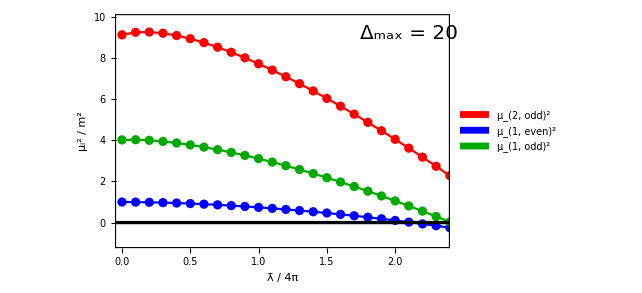

```mathematica
zero=Plot[0,{x,-0.1Max[λlist],1.1Max[λlist]},PlotStyle->{Black,Thickness[0.005]}];
data=Flatten[{dataOdd,dataEven},1];
exper=ListPlot[data,Frame->True,FrameStyle->Thickness[0.002],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["λ̄ / 4π",FontFamily->"Times",FontSize->20,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->20,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475,PlotRange->{{0,2.35},{-1,9.9}},Epilog->{Inset[Style["Δ_max = "<>ToString[Dmax],FontFamily->"Times",FontSize->20],{2.1,9.2}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2","μ_(1, even)^2","μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.6}]];
fit=ListLinePlot[data,PlotStyle->{{Red},{Blue},{Darker[Green]}},InterpolationOrder->1,PlotRange->All];
Show[exper,fit,zero]
```

## Convergence with Δ_max (Figure 13)

## Load Data

```mathematica
(* Load Hamiltonian matrices. These matrices include both odd and even particle-number states. *)
binaryGet[name_]:=Import[name]//BinaryDeserialize;
SetDirectory[NotebookDirectory[]];
fullMassMatrix=binaryGet["ScalarMassD"<>ToString[DMAX]<>".WXF"];                        (* Mass Matrix *)
fullNtoNMatrix=binaryGet["ScalarPhi4NtoND"<>ToString[DMAX]<>".WXF"];               (* ϕ^4(n->n) *)
fullNtoN2Matrix=binaryGet["ScalarPhi4NtoN2D"<>ToString[DMAX]<>".WXF"];          (* ϕ^4(n->n+2) *)
```

## Compute Mass Gap vs Δ_max for Odd-Particle Sector

### Define useful functions

```mathematica
(* 'massFuncOdd' extracts the mass matrix for the odd-particle-number sector given 'fullMassMatrix'.
DMAX = max scaling dimension in 'fullMassMatrix'.
Dmax = desired Δmax to study (should be ≤ DMAX). *) 
massFuncOdd[DMAX_,Dmax_]:=Module[{i,j,Nmax,count,COUNT,massTemp},
Nmax=Ceiling[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n-1}]//Length,{n,Nmax}];
COUNT=Accumulate[Table[IntegerPartitions[DMAX,{n}]//Length,{n,0,2Nmax-2}]][[;;;;2]];
massTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(* 'intFuncOdd' extracts the ϕ^4 interaction matrix for the odd-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix'.
DMAX = max scaling dimension in 'fullNtoNMatrix' and 'fullNtoN2Matrix'.
Dmax = desired Δmax to study (should be ≤ DMAX). *)
intFuncOdd[DMAX_,Dmax_]:=Module[{i,j,Nmax,count,COUNT,intTemp},
Nmax=Ceiling[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n-1}]//Length,{n,Nmax}];
COUNT=Accumulate[Table[IntegerPartitions[DMAX,{n}]//Length,{n,0,2Nmax-2}]][[;;;;2]];
intTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=fullNtoNMatrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i+1]]+1;;COUNT[[i+1]]+count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[COUNT[[i+1]]+1;;COUNT[[i+1]]+count[[i+1]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];
```

### Compute lowest eigenvalues vs Δ_max

```mathematica
(* For a chosen coupling λ, compute low eigenvalues vs Subscript[Δ, max] and store data as a list in valListOdd *)
```

```mathematica
Dlist=Table[Δmax,{Δmax,10,20}];    (* List of Δmax we want to study  *)
nPoints=2;                                                      (* Number of low eigenvalues to compute for each value of Δmax *)

(* To efficiently compute the lowest eigenvalues, it is useful if all eigenvalues are positive. To ensure all eigenvalues are positive, we can add a small overall shift to the eigenvalues before diagonalizing the Hamitonian, then remove this shift after diagonalizing. This shift needs to be large enough to overcome any negative eigenvalues, but small enough to not decrease the precision of the resulting eigenvalues (in practice 50 is generally a safe value) *)
shift=50;

m=1;
λ=0.55;                                                              (* Set value of the coupling *) 
valListOdd=Table[{},{i,Length[Dlist]}];
Monitor[For[iD=1,iD≤Length[Dlist],iD++,
mass=massFuncOdd[DMAX,Dlist[[iD]]];
int=intFuncOdd[DMAX,Dlist[[iD]]];
vals=Eigenvalues[SparseArray[N[full[m^2,4π λ,mass,int]+shift*IdentityMatrix[mass//Length]]],-nPoints,Method->"Arnoldi"];
valListOdd[[iD]]=vals-shift;
],{iD}];
```

## Compute Mass Gap vs Δ_max for Even-Particle Sector

### Define useful functions

```mathematica
(* 'massFuncEven' extracts the mass matrix for the even-particle-number sector given 'fullMassMatrix'.
DMAX = max scaling dimension in 'fullMassMatrix'.
Dmax = desired Δmax to study (should be ≤ DMAX). *) 
massFuncEven[DMAX_,Dmax_]:=Module[{i,j,Nmax,count,COUNT,massTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
COUNT=Accumulate[Table[IntegerPartitions[DMAX,{n}]//Length,{n,1,2Nmax-1}]][[;;;;2]];
massTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(* 'intFuncEven' extracts the ϕ^4 interaction matrix for the even-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix'.
DMAX = max scaling dimension in 'fullNtoNMatrix' and 'fullNtoN2Matrix'.
Dmax = desired Δmax to study (should be ≤ DMAX). *)
intFuncEven[DMAX_,Dmax_]:=Module[{i,j,Nmax,count,COUNT,intTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
COUNT=Accumulate[Table[IntegerPartitions[DMAX,{n}]//Length,{n,1,2Nmax-1}]][[;;;;2]];
intTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=fullNtoNMatrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i+1]]+1;;COUNT[[i+1]]+count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[COUNT[[i+1]]+1;;COUNT[[i+1]]+count[[i+1]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];
```

### Compute lowest eigenvalues vs Δ_max

```mathematica
(* For a chosen coupling λ, compute low eigenvalues vs Subscript[Δ, max] and store data as a list in valListEven *)
```

```mathematica
Dlist=Table[Δmax,{Δmax,10,20}];       (* List of Δmax we want to study  *)
nPoints=1;                                                           (* Number of low eigenvalues to compute for each value of Δmax *)

(* To efficiently compute the lowest eigenvalues, it is useful if all eigenvalues are positive. To ensure all eigenvalues are positive, we can add a small overall shift to the eigenvalues before diagonalizing the Hamitonian, then remove this shift after diagonalizing. This shift needs to be large enough to overcome any negative eigenvalues, but small enough to not decrease the precision of the resulting eigenvalues (in practice 50 is generally a safe value) *)
shift=50;

m=1;
λ=0.55;                                                                  (* Set value of the coupling *) 
valListEven=Table[{},{i,Length[Dlist]}];
Monitor[For[iD=1,iD≤Length[Dlist],iD++,
mass=massFuncEven[DMAX,Dlist[[iD]]];
int=intFuncEven[DMAX,Dlist[[iD]]];
vals=Eigenvalues[SparseArray[N[full[m^2,4π λ,mass,int]+shift*IdentityMatrix[mass//Length]]],-nPoints,Method->"Arnoldi"];
valListEven[[iD]]=vals-shift;
],{iD}];
```

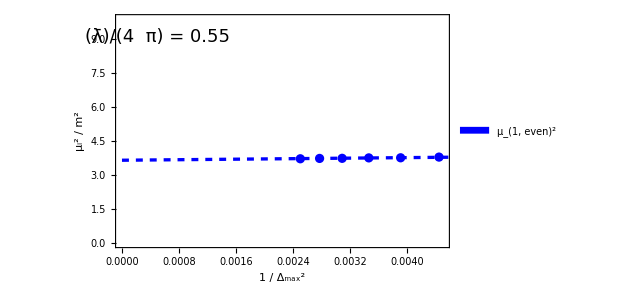

```mathematica
data={Thread[{1/Dlist^2,valListEven[[All,1]]}]};
fit1=FindFit[Thread[{1/Dlist^2,valListEven[[All,1]]}],a+b*x,{a,b},x];
exper=ListPlot[data,Frame->True,FrameStyle->Thickness[0.002],PlotStyle->{{Blue,PointSize[0.014]}},FrameLabel->{Style["1 / Δ_max^2",FontFamily->"Times",FontSize->18,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->18,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475,PlotRange->{{0,0.0045},{0,9.9}},Epilog->{Inset[Style["(λ̄)/(4  π) = 0.55",FontFamily->"Times",FontSize->18],{0.0005,9.11}]},PlotLegends->Placed[SwatchLegend[{"μ_(1, even)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.65}]];
line=Plot[{(a+b*x)/.fit1},{x,0,1.05*Max[1/Dlist^2]},PlotStyle->{{Blue,Dashed,Thickness[0.005]}}];
Show[exper,line]
```

## Create Figure 13

```mathematica
(* To make plot at a given coupling, set λ as desired when running the Odd- and Even- sector codes above. 
The output of the codes above are 'valListOdd' and 'valListEven', which store the low evals vs Subscript[Δ, max] for the chosen value of λ.
 For plotting, set p below to define horizontal axis in plot to be (Subscript[Δ, max])^-p. For small coupling, p=2 approximately,
   while for near-critical coupling p=1 seems to be a better fit.
   
The example plot below is for λ=0.55 with 10 ≤ Subscript[Δ, max] ≤ 20 and setting p=2. 
*)
```

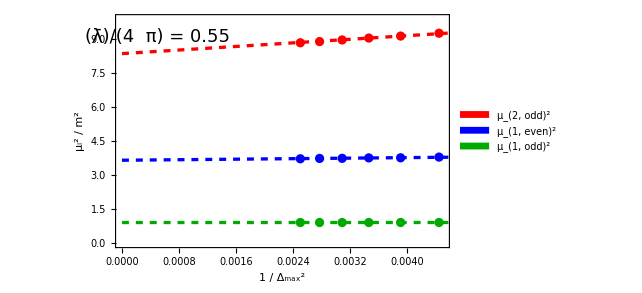

```mathematica
one=valListOdd[[All,2]];                      (* Lowest odd eval vs. Subscript[Δ, max] *) 
two=valListEven[[All,1]];                   (* Lowest even eval vs. Subscript[Δ, max] *) 
three=valListOdd[[All,1]];                 (* 2nd-lowest odd eval vs. Subscript[Δ, max] *) 
p=2;                                                                     (* Define horizontal axis in plot to be (Subscript[Δ, max])^-p *)

data={Thread[{1/Dlist^p,three}],Thread[{1/Dlist^p,two}],Thread[{1/Dlist^p,one}]};
fit1=FindFit[Thread[{1/Dlist^p,one}],a+b*x,{a,b},x];
fit2=FindFit[Thread[{1/Dlist^p,two}],a+b*x,{a,b},x];
fit3=FindFit[Thread[{1/Dlist^p,three}],a+b*x,{a,b},x];
exper=ListPlot[data,Frame->True,FrameStyle->Thickness[0.002],PlotStyle->{{Red,PointSize[0.014]},{Blue,PointSize[0.014]},{Darker[Green],PointSize[0.014]}},FrameLabel->{Style["1 / Δ_max^2",FontFamily->"Times",FontSize->18,FontColor->Black],Style["μ_i^2 / m^2",FontFamily->"Times",FontSize->18,FontColor->Black],None,None},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475,PlotRange->{{0,0.0045},{0,9.9}},Epilog->{Inset[Style["(λ̄)/(4  π) = 0.55",FontFamily->"Times",FontSize->18],{0.0005,9.11}]},PlotLegends->Placed[SwatchLegend[{"μ_(2, odd)^2","μ_(1, even)^2","μ_(1, odd)^2"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",5}],{0.9,0.65}]];
line=Plot[{(a+b*x)/.fit3,(a+b*x)/.fit2,(a+b*x)/.fit1},{x,0,1.05*Max[1/Dlist^p]},PlotStyle->{{Red,Dashed,Thickness[0.005]},{Blue,Dashed,Thickness[0.005]},{Darker[Green],Dashed,Thickness[0.005]}}];
Show[exper,line]
```

## Spectral Densities (Figures 14 - 17)

## Compute Overlaps with Basis States

ONLY NEEDS TO BE RUN ONCE FOR A GIVEN DMAX

To compute spectral densities for an operator (such as ϕ^n), we first need the overlaps of our basis states with that operator. This section loads the primary operator basis and computes the overlap of the basis states with ϕ^n up to some maximum value of n (set below). The overlaps are then saved, and can be loaded to compute spectral densities. This procedure only needs to be run once for a given value of DMAX (once the basis has been constructed).

### Load Basis

```mathematica
(* This function converts WXF files into a usable format *)
binaryGet[name_]:=Import[name]//BinaryDeserialize;

(* Load the basis *)
basis=binaryGet["BasisBosonD"<>ToString[DMAX]<>".WXF"];
```

### Compute Overlaps of Basis with ϕ^n

```mathematica
(* Set maximum particle number to compute overlap with ϕ^n *)
nMax=6;

(* Define function computing overlap of ϕ^n with single monomial *)
overlapMono[k_,n_]:=(n!)/Gamma[Total[k]] √((Gamma[2Total[k]]Length[Permutations[k]])/((4π)^(n-1)Length[k]!(Times@@k)))//N;

(* Create a placeholder for the list of basis state overlaps *)
overlaps=ConstantArray[{},nMax];

(* There is only one single-particle state (∂ϕ), with a trivial overlap with ϕ *)
overlaps[[1]]={1};

(* Proceed by particle number up to nMax *)
Monitor[For[nPart=2,nPart≤nMax,nPart++,
temp={};
(* For each particle number, proceed by scaling dimension up to DMAX *)
For[Δ=nPart,Δ≤DMAX,Δ++,
(* Construct the list of monomials at this particle number and degree *)
klist=IntegerPartitions[Δ,{nPart}];
(* Extract the coefficients of the primary basis states in terms of monomials *)
coeffs=basis[[1,Δ-nPart+1,nPart]];
If[Length[coeffs]>0,
(* First compute a table of overlaps of monomials with ϕ^n *)
overlapArray=Table[overlapMono[k,nPart],{k,klist}];
(* Use this array to obtain the overlap of basis states with ϕ^n *)
temp=Join[temp,coeffs.overlapArray];
];
];
overlaps[[nPart]]=temp;
],{nPart,Δ}];

(* Save the resulting overlaps *)
DeleteFile["OverlapsD"<>ToString[DMAX]];
Save["OverlapsD"<>ToString[DMAX],{overlaps}];
```

DeleteFile::fdnfnd: Directory or file OverlapsD20 not found.

## Diagonalize Hamiltonian and Compute Spectral Densities

RUN THIS SECTION BEFORE CREATING FIGURES

### Load Data

```mathematica
(* This function converts WXF files into a usable format *)
binaryGet[name_]:=Import[name]//BinaryDeserialize;

(* Load mass term and ϕ^4 interaction matrices *)
fullMassMatrix=binaryGet["ScalarMassD"<>ToString[DMAX]<>".WXF"];
fullNtoNMatrix=binaryGet["ScalarPhi4NtoND"<>ToString[DMAX]<>".WXF"];
fullNtoN2Matrix=binaryGet["ScalarPhi4NtoN2D"<>ToString[DMAX]<>".WXF"];

(* Load overlaps of basis states with ϕ^n *)
overlaps=Get["OverlapsD"<>ToString[DMAX]];
```

### Define Useful Functions

```mathematica
(*
	'massFuncEven' extracts the mass matrix for the even-particle-number sector given 'fullMassMatrix'.
DMAX = max scaling dimension in 'fullMassMatrix'.
Dmax = desired Δmax to study (should be ≤ DMAX).
*) 
massFuncEven[DMAX_,Dmax_]:=Module[{i,j,Nmax,count,COUNT,massTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
COUNT=Accumulate[Table[IntegerPartitions[DMAX,{n}]//Length,{n,1,2Nmax-1}]][[;;;;2]];
massTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(*
	'intFuncEven' extracts the ϕ^4 interaction matrix for the even-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix'.
DMAX = max scaling dimension in 'fullNtoNMatrix' and 'fullNtoN2Matrix'.
Dmax = desired Δmax to study (should be ≤ DMAX).
*)
intFuncEven[DMAX_,Dmax_]:=Module[{i,j,Nmax,count,COUNT,intTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
COUNT=Accumulate[Table[IntegerPartitions[DMAX,{n}]//Length,{n,1,2Nmax-1}]][[;;;;2]];
intTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=fullNtoNMatrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i+1]]+1;;COUNT[[i+1]]+count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[COUNT[[i+1]]+1;;COUNT[[i+1]]+count[[i+1]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];

(* Modified version of Eigensystem which sorts the eigenvalues by actual value (rather than absolute value) *)
eigensys[mat_]:=Eigensystem[mat]//Transpose//Sort//Transpose;

(* Location of the first and last basis state of a given particle number in the full list of basis states at Dmax *)
first[n_,Dmax_]:=Sum[IntegerPartitions[Dmax,{nPart}]//Length,{nPart,2,n-2,2}]+1;
last[n_,Dmax_]:=Sum[IntegerPartitions[Dmax,{nPart}]//Length,{nPart,2,n,2}];

(* Compute the overlaps of ϕ^n with a list of vectors (vecs_) written in the primary operator basis, to obtain the integrated spectral density *)
ϕspec[n_,Dmax_,vecs_]:=Table[overlaps[[n,1;;last[n,Dmax]-first[n,Dmax]+1]].vecs[[i,first[n,Dmax];;last[n,Dmax]]],{i,Length[vecs]}];
ϕspecSum[n_,Dmax_,vecs_]:=Accumulate[Abs[ϕspec[n,Dmax,vecs]]^2];

(* Compute the overlaps of (∂ϕ)^n with a list of vectors (vecs_) written in the primary operator basis, to obtain the integrated spectral density *)
dϕspec[n_,Dmax_,vecs_]:=Table[vecs[[i,first[n,Dmax]]],{i,Length[vecs]}];
dϕspecSum[n_,Dmax_,vecs_]:=Accumulate[Abs[dϕspec[n,Dmax,vecs]]^2];

(* Compute the overlaps of T_(+-)=(1/2 m^2+1/(16π)λ)ϕ^2+1/(4!)λϕ^4 with a list of vectors (vecs_) written in the primary operator basis, to obtain the integrated spectral density. *)
Tspec[msq_,λ_,Dmax_,vecs_]:=Table[(1/2*msq+1/(16π)*λ)*overlaps[[2,1;;last[2,Dmax]-first[2,Dmax]+1]].vecs[[i,first[2,Dmax];;last[2,Dmax]]]+1/(4!)*λ*overlaps[[4,1;;last[4,Dmax]-first[4,Dmax]+1]].vecs[[i,first[4,Dmax];;last[4,Dmax]]],{i,Length[vecs]}];
TspecSum[msq_,λ_,Dmax_,vecs_]:=Accumulate[Abs[Tspec[msq,λ,Dmax,vecs]]^2];
```

### Set Values for Δmax, Diagonalize Hamiltonian, and Compute Spectral Densities

```mathematica
(*
When comparing spectral densities for different values of Δmax, it is better to keep the mass gap fixed, rather than the coupling. Here we have saved the values of the coupling needed to obtain particular fixed values for the mass gap, which correspond to the mass gap values used in Figures 14-17 in the paper:

	Subscript[μ, gap]^2 = 0.288:
	DmaxList={10,15,20,30,40};
		λlist={2.9779124867558213,2.534117271143702,2.3034016936411357,2.1016431454200872,2.};

		Subscript[μ, gap]^2 = 0.036:
	DmaxList={10,15,20,30,40};
		λlist={3.1147954147490458,2.642161637820305,2.3982297851939047,2.18003874441386,2.07};

We have provided a section below entitled "Extract Coupling as a Function of Mass Gap (at Fixed Δmax)", which allows the user to compute the coupling needed to obtain any particular value of the mass gap at various Δmax.
*)
```

```mathematica
(* Set the values of Δmax (≤DMAX) to consider, and the corresponding value for the coupling *)
DmaxList={10,15,20};
λlist={2.9779124867558213,2.534117271143702,2.3034016936411357};

(* Set the maximum number of low-energy eigenvalues to include in the spectral density *)
nPointsMax=1000;

(* Create placeholders for the eigenvalues, C-function, and spectral density for T_(+-) *)
valList=ConstantArray[{},Length[DmaxList]];
specCList=ConstantArray[{},Length[DmaxList]];
specTList=ConstantArray[{},Length[DmaxList]];

(* Proceed through each value of Δmax, diagonalizing the Hamiltonian and computing the spectral densities *)
For[iD=1,iD≤Length[DmaxList],iD++,
Dmax=DmaxList[[iD]];
λ=λlist[[iD]];
Print["Δmax = "<>ToString[Dmax]];

mass=massFuncEven[DMAX,Dmax];
int=intFuncEven[DMAX,Dmax];

nPoints=Min[nPointsMax,Length[mass]];
m=1;

t1=AbsoluteTime[];
Print["Diagonalizing Matrix..."];
{vals,vecs}=eigensys[full[m^2,4π λ,mass,int]];
Print["Diagonalized!"];
valList[[iD]]=vals[[1;;nPoints]];
specCList[[iD]]=dϕspecSum[2,Dmax,vecs][[1;;nPoints]];
specTList[[iD]]=TspecSum[m^2,4π λ,Dmax,vecs][[1;;nPoints]];
t2=AbsoluteTime[];
Print["Time Elapsed: "<>ToString[(t2-t1)/60]];
];
```

Δmax = 10

Diagonalizing Matrix...

Diagonalized!

Time Elapsed: 0.00029202

Δmax = 15

Diagonalizing Matrix...

Diagonalized!

Time Elapsed: 0.00023423

Δmax = 20

Diagonalizing Matrix...

Diagonalized!

Time Elapsed: 0.00193322

## Create Figure 14

Plot the C-function for the different values of Δmax

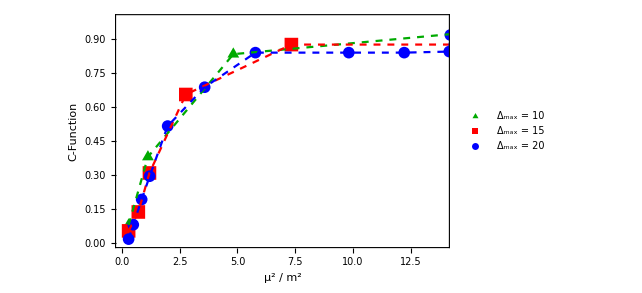

```mathematica
dataFig14=ListPlot[Table[Thread[{valList[[iD]],specCList[[iD]]}],{iD,Length[DmaxList]}],Frame->True,FrameStyle->Thickness[0.002],FrameLabel->{Style["μ^2 / m^2",FontFamily->"Times",FontSize->18,FontColor->Black],Style["C-Function",FontFamily->"Times",FontSize->18,FontColor->Black],None,None},PlotStyle->{Darker[Green],Red,Blue},PlotMarkers->{{▲,14},{■,14},{●,12}},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475,PlotRange->{{0,13.9},{0,0.99}},PlotLegends->Placed[PointLegend[Table["Δ_max = "<>ToString[DmaxList[[iD]]],{iD,Length[DmaxList]}],LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",Length[DmaxList]}],{0.85,0.25}]];
fitFig14=ListLinePlot[Table[Thread[{valList[[iD]],specCList[[iD]]}],{iD,Length[DmaxList]}],PlotStyle->{{Darker[Green],Dashed},{Red,Dashed},{Blue,Dashed}},InterpolationOrder->1,PlotRange->All];
Show[dataFig14,fitFig14]
```

## Create Figure 15

Plot the IR behavior of the C-function, compared with theoretical predictions from the 2D Ising model. The Ising prediction has one free parameter (Λ), which controls the correction due to the higher-dimensional operator ∂^2 ϵ.

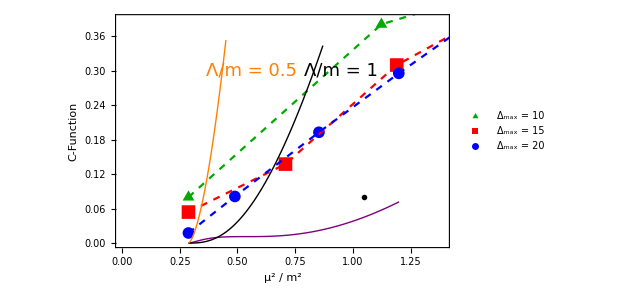

```mathematica
(* Ising model prediction for the IR behavior of the C-function, which depends on the unknown parameter Λ *)
Cfunc[Λ_,x_]:=1/2 (1-valList[[-1,1]]/x)^(3/2)+(3 √(1-valList[[-1,1]]/x) x+(3valList[[-1,1]])/2 (Log[valList[[-1,1]]/2]-Log[-valList[[-1,1]]/2+x+√(1-valList[[-1,1]]/x) x]))/Λ^2+(3 √valList[[-1,1]](2 √(1-valList[[-1,1]]/x)+Log[valList[[-1,1]]/2]-Log[-valList[[-1,1]]/2+x+√(1-valList[[-1,1]]/x) x]))/Λ;

(* Create Ising prediction plots for Λ=2,1,0.5 (in units of the bare mass) *)
Ctheory1=
Plot[{Cfunc[2,x]},{x,valList[[-1,1]],1.2},PlotStyle->{{Purple,Thick}},PlotRange->All];
Ctheory2=
Plot[{Cfunc[1,x]},{x,valList[[-1,1]],0.87},PlotStyle->{{Black,Thick}},PlotRange->All];
Ctheory3=
Plot[{Cfunc[0.5,x]},{x,valList[[-1,1]],0.45},PlotStyle->{{Orange,Thick}},PlotRange->All];

(* Plot C-function for different values of Δmax *)
dataFig15=ListPlot[Table[Thread[{valList[[iD]],specCList[[iD]]}],{iD,Length[DmaxList]}],Frame->True,FrameStyle->Thickness[0.002],FrameLabel->{Style["μ^2 / m^2",FontFamily->"Times",FontSize->18,FontColor->Black],Style["C-Function",FontFamily->"Times",FontSize->18,FontColor->Black],None,None},PlotStyle->{Darker[Green],Red,Blue},PlotMarkers->{{▲,14},{■,14},{●,12}},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475,PlotRange->{{0,1.39},{0,0.39}},Epilog->{Inset[Style["Λ/m = 1",FontFamily->"Times",FontSize->18,FontColor->Black],{0.95,0.3}],Inset[Style["Λ/m = 0.5",FontFamily->"Times",FontSize->18,FontColor->Orange],{0.56,0.3}],Inset[Style["Λ/m = 2",FontFamily->"Times",FontSize->18,FontColor->Purple],{1.05,0.08}]},PlotLegends->Placed[PointLegend[Table["Δ_max = "<>ToString[DmaxList[[iD]]],{iD,Length[DmaxList]}],LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",Length[DmaxList]}],{0.14,0.7}]];
fitFig15=ListLinePlot[Table[Thread[{valList[[iD]],specCList[[iD]]}],{iD,Length[DmaxList]}],PlotStyle->{{Darker[Green],Dashed},{Red,Dashed},{Blue,Dashed}},InterpolationOrder->1,PlotRange->All];
Show[dataFig15,fitFig15,Ctheory1,Ctheory2,Ctheory3]
```

## Create Figure 16

Plot the IR behavior of the C-function, with the correction from ∂^2 ϵ removed, and compare with the Ising model prediction.

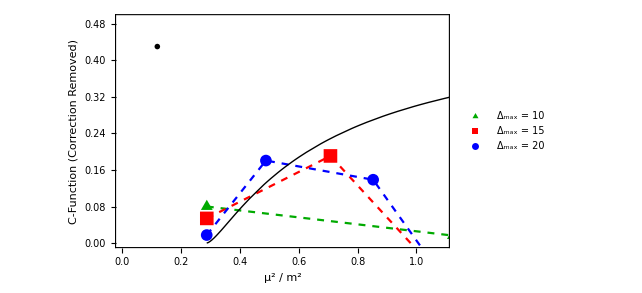

```mathematica
(* Set the parameter Λ *)
Λ=1;

(* Theoretical prediction for correction from ∂^2 ϵ, which depends on Λ *)
Ccorr[Λ_,x_]:=(3 √(1-valList[[-1,1]]/x) x+(3valList[[-1,1]])/2 (Log[valList[[-1,1]]/2]-Log[-valList[[-1,1]]/2+x+√(1-valList[[-1,1]]/x) x]))/Λ^2+(3 √valList[[-1,1]](2 √(1-valList[[-1,1]]/x)+Log[valList[[-1,1]]/2]-Log[-valList[[-1,1]]/2+x+√(1-valList[[-1,1]]/x) x]))/Λ;

(* Uncorrected Ising model prediction *)
Cising[x_]:=1/2 (1-valList[[-1,1]]/x)^(3/2);
Ctheory=Plot[Cising[x],{x,valList[[-1,1]],20},PlotStyle->{Black,Thick},PlotRange->All];

(* Correct truncation data by removing the theoretical prediction for the ∂^2 ϵ contribution *)
corrData=Table[{valList[[iD,iV]],specCList[[iD,iV]]-Ccorr[Λ,valList[[iD,iV]]]},{iD,Length[DmaxList]},{iV,Length[valList[[iD]]]}];

(* Plot corrected IR behavior for C-function, compared with Ising model prediction *)
dataFig16=ListPlot[corrData,Frame->True,FrameStyle->Thickness[0.002],FrameLabel->{Style["μ^2 / m^2",FontFamily->"Times",FontSize->18,FontColor->Black],Style["C-Function (Correction Removed)",FontFamily->"Times",FontSize->18,FontColor->Black],None,None},PlotStyle->{Darker[Green],Red,Blue},PlotMarkers->{{▲,14},{■,14},{●,12}},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475,PlotRange->{{0,1.09},{0,0.49}},Epilog->{Inset[Style["Λ/m = 1",FontFamily->"Times",FontSize->18,FontColor->Black],{0.12,0.43}]},PlotLegends->Placed[PointLegend[Table["Δ_max = "<>ToString[DmaxList[[iD]]],{iD,Length[DmaxList]}],LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",Length[DmaxList]}],{0.15,0.6}]];
fitFig16=ListLinePlot[corrData,PlotStyle->{{Darker[Green],Dashed},{Red,Dashed},{Blue,Dashed}},InterpolationOrder->1,PlotRange->All];
Show[dataFig16,fitFig16,Ctheory]
```

## Create Figure 17

Plot the integrated spectral density of T_(+_) for the different values of Δmax

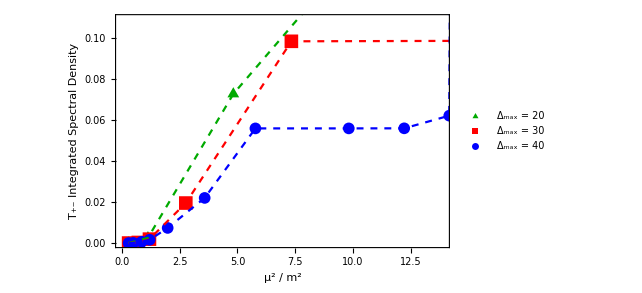

```mathematica
dataFig17=ListPlot[Table[Thread[{valList[[iD]],specTList[[iD]]}],{iD,Length[DmaxList]}],Frame->True,FrameStyle->Thickness[0.002],FrameLabel->{Style["μ^2 / m^2",FontFamily->"Times",FontSize->18,FontColor->Black],Style["T_(+-) Integrated Spectral Density",FontFamily->"Times",FontSize->18,FontColor->Black],None,None},PlotStyle->{Darker[Green],Red,Blue},PlotMarkers->{{▲,14},{■,14},{●,12}},FrameTicksStyle->14,LabelStyle->Black,ImageSize->475,PlotRange->{{0,13.9},{0,0.109}},PlotLegends->Placed[PointLegend[{"Δ_max = 20","Δ_max = 30","Δ_max = 40"},LabelStyle->{FontFamily->"Times",18},LegendLayout->{"Row",3}],{0.14,0.75}]];
fitFig17=ListLinePlot[Table[Thread[{valList[[iD]],specTList[[iD]]}],{iD,Length[DmaxList]}],PlotStyle->{{Darker[Green],Dashed},{Red,Dashed},{Blue,Dashed}},InterpolationOrder->1,PlotRange->All];
Show[dataFig17,fitFig17]
```

## Extract Coupling as a Function of Mass Gap (at Fixed Δmax)

To compare spectral densities at different values of Δmax, we need to determine the value of the coupling for each Δmax which corresponds to some fixed value of the mass gap. This section scans over values of the coupling, diagonalizing the Hamiltonian at each value, in order to construct an interpolating function that can be used to determine the value of the coupling needed to compute any mass gap.

### Load Data

```mathematica
(* This function converts WXF files into a usable format *)
binaryGet[name_]:=Import[name]//BinaryDeserialize;

(* Load mass term and ϕ^4 interaction matrices *)
fullMassMatrix=binaryGet["ScalarMassD"<>ToString[DMAX]<>".WXF"];
fullNtoNMatrix=binaryGet["ScalarPhi4NtoND"<>ToString[DMAX]<>".WXF"];
fullNtoN2Matrix=binaryGet["ScalarPhi4NtoN2D"<>ToString[DMAX]<>".WXF"];

(* Load overlaps of basis states with ϕ^n *)
overlaps=Get["OverlapsD"<>ToString[DMAX]];
```

### Define Useful Functions

```mathematica
(*
	'massFuncEven' extracts the mass matrix for the even-particle-number sector given 'fullMassMatrix'.
DMAX = max scaling dimension in 'fullMassMatrix'.
Dmax = desired Δmax to study (should be ≤ DMAX).
*) 
massFuncEven[DMAX_,Dmax_]:=Module[{i,j,Nmax,count,COUNT,massTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
COUNT=Accumulate[Table[IntegerPartitions[DMAX,{n}]//Length,{n,1,2Nmax-1}]][[;;;;2]];
massTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
massTemp[[i,i]]=fullMassMatrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
For[j=i+1,j≤Nmax,j++,
massTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
massTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[massTemp],{{}...},Infinity]//N//Chop
];

(*
	'intFuncEven' extracts the ϕ^4 interaction matrix for the even-particle-number sector given 'fullNtoNMatrix' and 'fullNtoN2Matrix'.
DMAX = max scaling dimension in 'fullNtoNMatrix' and 'fullNtoN2Matrix'.
Dmax = desired Δmax to study (should be ≤ DMAX).
*)
intFuncEven[DMAX_,Dmax_]:=Module[{i,j,Nmax,count,COUNT,intTemp},
Nmax=Floor[Dmax/2];
count=Table[IntegerPartitions[Dmax,{2n}]//Length,{n,Nmax}];
COUNT=Accumulate[Table[IntegerPartitions[DMAX,{n}]//Length,{n,1,2Nmax-1}]][[;;;;2]];
intTemp=ConstantArray[0,{Nmax,Nmax}];
For[i=1,i≤Nmax,i++,
intTemp[[i,i]]=fullNtoNMatrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
If[i≤Nmax-1,
intTemp[[i,i+1]]=fullNtoN2Matrix[[COUNT[[i]]+1;;COUNT[[i]]+count[[i]],COUNT[[i+1]]+1;;COUNT[[i+1]]+count[[i+1]]]];
intTemp[[i+1,i]]=fullNtoN2Matrix[[COUNT[[i+1]]+1;;COUNT[[i+1]]+count[[i+1]],COUNT[[i]]+1;;COUNT[[i]]+count[[i]]]];
];
For[j=i+2,j≤Nmax,j++,
intTemp[[i,j]]=ConstantArray[0,{count[[i]],count[[j]]}];
intTemp[[j,i]]=ConstantArray[0,{count[[j]],count[[i]]}];
];
];
DeleteCases[ArrayFlatten[intTemp],{{}...},Infinity]//N//Chop
];

(* 'full' defines the full Hamiltonian, where full = msq*1/2 ϕ^2 + λ*1/(4!)ϕ^4 *) 
full[msq_,λ_,mass_,int_]:=N[msq*mass+λ*int];
```

### Set Δmax and Desired Mass Gap and Scan over Couplings

```mathematica
(* Set the value of Δmax *)
Dmax=15;

(* Set the desired mass gap Subscript[μ, gap]^2 (in units of the bare mass) *)
gapGoal=0.036;

(* Scan over values of the coupling, computing the mass gap at each value *)
m=1;
λmax=4;
λmin=0.;
λcount=200;
dλ=(λmax-λmin)/(λcount-1)//N;
λlist=Table[λmin+dλ*(i-1),{i,λcount}];
shift=50;
mass=massFuncEven[DMAX,Dmax];
int=intFuncEven[DMAX,Dmax];
gapList=Table[{},{i,Length[λlist]}];
Monitor[For[iL=1,iL≤Length[λlist],iL++,
vals=Eigenvalues[SparseArray[N[full[m^2,4π λlist[[iL]],mass,int]+shift*IdentityMatrix[mass//Length]]],-1,Method->"Arnoldi"];
gapList[[iL]]=vals-shift;
],{iL}];

(* Create an interpolating function based on the data, which can be used to determine the needed value of the coupling for any mass gap *)
coupling=Interpolation[Thread[{gapList,λlist}]];

(* Compute the coupling needed for the desired mass gap *)
coupling[gapGoal]
```

2.64216